```mathematica
PicSize=6;
AFITSizeFac=1.38;
AFITAspectRatio=1/GoldenRatio;
AFITFontSize=12;
AFITImageSize=72*PicSize*AFITSizeFac;
LeftPad=72;
RightPad=72;
BottomPad=48;
TopPad=16;
```

```mathematica
AFITPlotOptions={Axes->False,Frame->True,FrameStyle->Black,AspectRatio->AFITAspectRatio,BaseStyle->{FontSize->AFITFontSize,FontFamily->"Helvetica",FontWeight->Plain,FontColor->Black},ImageSize->AFITImageSize,ImagePadding->{{LeftPad,RightPad},{BottomPad,TopPad}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed]};
```

```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
A1=4.45813734;
A2=0.200859853;
B1=0.467216334;
B2=0.391371166;
C1=2.89566290;
C2=47.1362108;
```

```mathematica
n[λ_]:=Module[{λ1},
λ1=Convert[λ,Micron]/Micron;
Return[√(1+(A1 λ1^2)/(λ1^2-A2^2)+(B1 λ1^2)/(λ1^2-B2^2)+(C1 λ1^2)/(λ1^2-C2^2))]]
```

```mathematica
nPlot=Plot[n[λ Micron],{λ,3,5}];
```

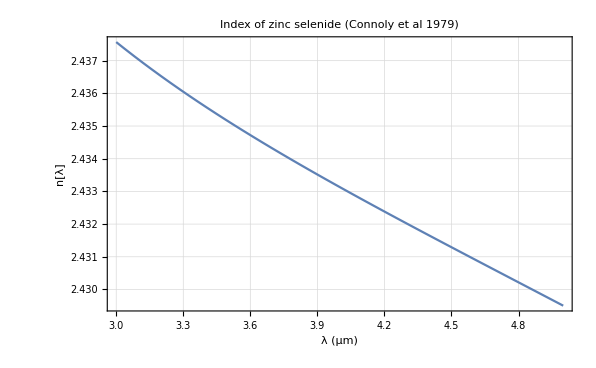

```mathematica
Show[nPlot,AFITPlotOptions,FrameLabel->{"λ (μm)","n[λ]"},PlotLabel->"Index of zinc selenide (Connoly et al 1979)"]
```

```mathematica
n[λ_]:=1.5
```

```mathematica
K=3100(Centi Meter/(Giga Watt)*ElectronVolt^(5/2));
```

```mathematica
c=SpeedOfLight;
```

```mathematica
Ep=21.4ElectronVolt;
```

```mathematica
h=PlanckConstant;
```

```mathematica
ℏ=h/(2π);
```

```mathematica
Eg=2.71ElectronVolt;
```

```mathematica
X[Eg_,λ_]:=(h c)/(λ Eg)
```

```mathematica
F2[x_]:=Re[(2x-1)^(3/2)/(2x)^5]
```

```mathematica
α2[λ_]:=Convert[(K √Ep)/(n[λ]^2 Eg^3)F2[X[Eg,λ]],Centimeter/(Giga Watt)]
```

```mathematica
α2Plot=Plot[α2[λ Micron]/(Centimeter/(Giga Watt)),{λ,0.4,5},PlotRange->All,PlotStyle->Black];
```

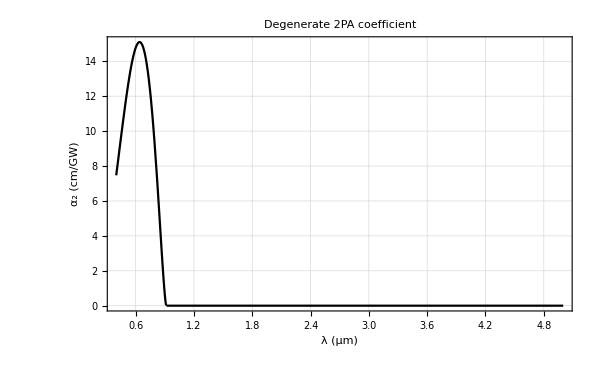

```mathematica
Show[α2Plot,AFITPlotOptions,FrameLabel->{"λ (μm)","α_2 (cm/GW)"},PlotLabel->"Degenerate 2PA coefficient"]
```

```mathematica
H[x1_,x2_]:=Re[1/(2^6 x1^4 x2^4)(5/16 x2^3 x1^2+9/8 x2^2 x1^2-9/4 x2 x1^2-3/4 x2^3-1/32 x2^3 x1^2(1-x1)^(-3/2)+1/2(x2+x1)^2((1-x2-x1)^(3/2)-(1-x1)^(3/2))-3/16 x2^2 x1^2((1-x1)^(-1/2)+(1-x2)^(-1/2))+3/2 x2 x1^2(1-x2)^(1/2)+3/2 x2^2 x1(1-x1)^(1/2)+3/4 x2(x2^2+x1^2)(1-x1)^(1/2)-3/8 x2^3 x1(1-x1)^(-1/2)+1/2(x2^2+x1^2)(1-(1-x2)^(3/2)))]
```

```mathematica
TPA[x1_,x2_]:=H[x1,x2]+H[-x1,x2]
```

```mathematica
RAM[x1_,x2_]:=H[x1,-x2]+H[-x1,-x2]
```

```mathematica
QSE[x1_]:=1/(2^9 x1^4)(3/4*((1-x1)^(-1/2)-(1+x1)^(-1/2))/x1-((1-x1)^(-3/2)+(1+x1)^(-3/2))/8-1/2)
```

```mathematica
G2[x1_,x2_]:=TPA[x1,x2]+RAM[x1,x2]+QSE[x1]
```

```mathematica
n2[λ_]:=Convert[(ℏ c K)/1(√Ep)/(n[λ]^2 Eg^4)G2[X[Eg,λ],X[Eg,λ]],Meter^2/Watt]
```

```mathematica
n2Plot=Plot[n2[λ Micron]/(Meter^2/Watt)*10^18,{λ,0,1},PlotRange->{-8,6},PlotStyle->Black];
```

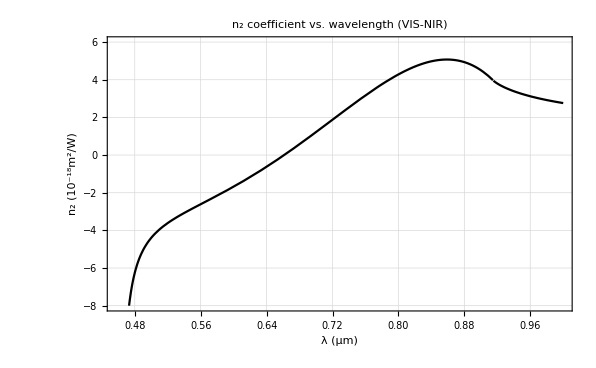

```mathematica
Show[n2Plot,AFITPlotOptions,FrameLabel->{"λ (μm)","n_2 (10^-18m^2/W)"},PlotLabel->"n_2 coefficient vs. wavelength (VIS-NIR)"]
```

```mathematica
n2Plot=Plot[n2[λ Micron]/(Meter^2/Watt)*10^18,{λ,1,5},PlotRange->{-8,6},PlotStyle->Blue];
```

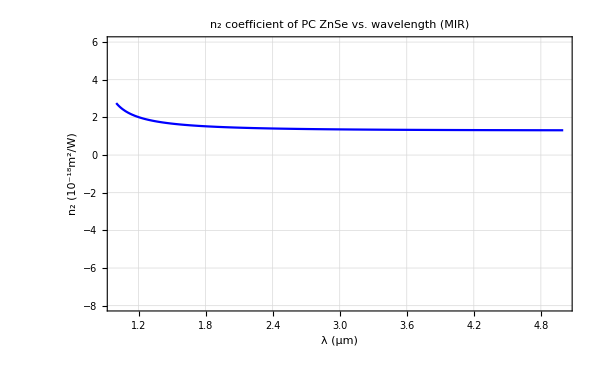

```mathematica
Show[n2Plot,AFITPlotOptions,FrameLabel->{"λ (μm)","n_2 (10^-18m^2/W)"},PlotLabel->"n_2 coefficient of PC ZnSe vs. wavelength (MIR)"]
```

```mathematica
α2theory=Chop[α2[3.8 Micron]]
```

0

```mathematica
n2theory=1Convert[n2[3.8 Micron],Centimeter^2/(Watt)]
```

(1.33355×10^-14 Centimeter^2)/Watt

```mathematica
Convert[n2theory,Meter^2/Watt]
```

(1.33355×10^-18 Meter^2)/Watt

```mathematica
n2table=Table[{λ,n2[λ Micron]/(Meter^2/Watt)*10^18},{λ,0.46,5,0.01}];
```

```mathematica
n2tablePlot=ListPlot[n2table,Joined->True,PlotRange->{-6,6}];
```

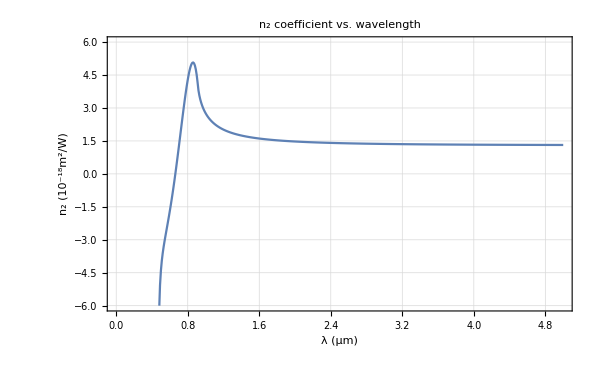

```mathematica
Show[n2tablePlot,AFITPlotOptions,FrameLabel->{"λ (μm)","n_2 (10^-18m^2/W)"},PlotLabel->"n_2 coefficient vs. wavelength"]
```